## Style

```mathematica
(*Styling of the text*)
st=Directive[FontSize->15,FontFamily->"CMU Serif"];
stylize[text_]:=Style[text,st];
glue[l1_,l2_]:=MapThread[{#1,#2}&,{l1,l2}];
BostonBlue=RGBColor["#00688B"];
```

## Inflation, substitution matrices and height statistics

Inflation creates new sites and new bonds. The old sites are all subsisting, but their coordination (their type) changes. The new sites are always nearest neighbors of at least one old site.
Evolution of the potential under inflation:
(1) The effect of inflation on the old tiles is to change the direction of the arrows along their edges (this is also true for Penrose, is it true in general?). Hence the potential on old sites only changes sign under inflation:
m_old^(l+1) = -m_old^(l)
(2) New sites are connected to old ones by one bond, and the arrow on this bond is always directed from new to old (or old to new, depending on the convention we choose). Hence,
m_new^(l+1) = m_old^(l+1)-1=-(m_old^(l)+1) 
Evolution of the statistics of the potential under inflation
Call N_μ^(l)(m) the number of times the potential takes value m on sites of type μ, after l inflations of a given starting pattern.
Then looking at (1) and (2) we get
N_μ^(l+1)(-m) = (M_0)_(μ,ν)N_ν^(l)(m) + (M_1)_(μ,ν)N_ν^(l)(m-1)

```mathematica
M0=SparseArray[{{1,1}->1,{1,2}->1,{1,3}->1,{1,4}->1,{2,5}->1,{3,6}->1,{4,7}->1},{7,7}]
```

SparseArray[<7>, {7, 7}]

```mathematica
M1=SparseArray[{{5,7}->1,{6,5}->2,{6,6}->3,{6,7}->2,{7,1}->8,{7,2}->8,{7,3}->8,{7,4}->8,{7,5}->5,{7,6}->2},{7,7}]
```

SparseArray[<10>, {7, 7}]

```mathematica
Eigensystem[M0.M1-M1.M0]
```

{{-2 √10,2 √10,0,0,0,0,0},{{0,-1/(2 √10),-1/(√10),1/5 (-5+2 √10),0,0,1},{0,1/(2 √10),1/(√10),1/5 (-5-2 √10),0,0,1},{-1,0,0,1,0,0,0},{-1,0,1,0,0,0,0},{-1,1,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}}}

```mathematica
Eigensystem[M0+M1]
```

{{3+2 √2,-3,1,3-2 √2,0,0,0},{{-(-2-√2)/((3+2 √2) (4+3 √2)),(√2)/((3+2 √2) (4+3 √2)),(2 (2+√2))/((3+2 √2) (4+3 √2)),1/(3+2 √2),(√2)/(4+3 √2),(2 (2+√2))/(4+3 √2),1},{1,3,2,-9,-9,-6,27},{0,1,-2,1,1,-2,1},{-(-2+√2)/((-3+2 √2) (-4+3 √2)),-(√2)/((-3+2 √2) (-4+3 √2)),-(2 (-2+√2))/((-3+2 √2) (-4+3 √2)),-1/(-3+2 √2),(√2)/(-4+3 √2),(2 (-2+√2))/(-4+3 √2),1},{-1,0,0,1,0,0,0},{-1,0,1,0,0,0,0},{-1,1,0,0,0,0,0}}}

```mathematica
Eigensystem[M0.M1+M1.M0]
```

{{2 (4+√6),-2 (-4+√6),0,0,0,0,0},{{0,1/(2 (4+√6)),1/(4+√6),(√6)/(4+√6),0,0,1},{0,-1/(2 (-4+√6)),-1/(-4+√6),(√6)/(-4+√6),0,0,1},{-1,0,0,1,0,0,0},{-1,0,1,0,0,0,0},{-1,1,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}}}

Note that M_0+M_1 is the geometric substitution matrix. Its largest eigenvalue is λ^2 (λ = 1+Sqrt[2]), and the entries of the associated eigenvector are the relative frequencies of the local environments.

```mathematica
(M0+M1)//MatrixForm
```

(1 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 2 | 3 | 2
8 | 8 | 8 | 8 | 5 | 2 | 0)

```mathematica
(* entries of the largest eigenvector *)
{val,vec}=Eigensystem[M0+M1];
μ=Sqrt[2]-1;
λ=1+Sqrt[2];
vec[[1]]μ//N
```

{0.0294373,0.0121933,0.0588745,0.0710678,0.0710678,0.343146,0.414214}

```mathematica
(* exact frequencies *)
f[1]=μ^4;
f[2]=μ^5;
f[3]=2μ^4;
f[4]=μ^3;
f[5]=μ^3;
f[6]=2μ^2;
f[7]=μ;
Table[N[f[i]],{i,7}]
```

{0.0294373,0.0121933,0.0588745,0.0710678,0.0710678,0.343146,0.414214}

```mathematica
Eigenvalues[M0]
Eigenvalues[M1]
```

{1,0,0,0,0,0,0}

{1+2 √3,1-2 √3,1,0,0,0,0}

```mathematica
(1+2Sqrt[3])/λ^2//N
```

0.765919

```mathematica
Eigenvectors[M0][[1]]
Eigenvectors[M1][[1]]
```

{1,0,0,0,0,0,0}

{0,0,0,0,-(-1+√3)/(-5+√3),-(2 (1+√3))/(-5+√3),1}

```mathematica
M0//MatrixForm
```

(1 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

### Moments of the distribution of heights, generalized inflation matrix, frequencies

We are interested in computing the moments of the distribution of heights:

(Ñ)_μ^(l)(t) = Σ_m t^m N_μ^(l)(m)
We have:
N_μ^(2l)(m) = (M_0)_(μ,ν)N_ν^(2l-1)(-m) + (M_1)_(μ,ν)N_ν^(2l-1)(-m-1)
and thus:
N_μ^(2l-1)(-m)         = (M_0)_(μ,ν)N_ν^(2l-2)(m) + (M_1)_(μ,ν)N_ν^(2l-2)(m-1) 
N_μ^(2l-1)(-m-1) = (M_0)_(μ,ν)N_ν^(2l-2)(m+1) + (M_1)_(μ,ν)N_ν^(2l-2)(m) 
So that,
N_μ^(2l)(m) = (M_0)_(μ,ν)((M_0)_(ν,σ)N_σ^(2l-2)(m) + (M_1)_(ν,σ)N_ν^(2l-2)(m-1) ) + (M_1)_(μ,ν)((M_0)_(ν,σ)N_σ^(2l-2)(m+1) + (M_1)_(ν,σ)N_σ^(2l-2)(m) )
and finally:
N_μ^(2l)(m) = (M_0^2+M_1^2)_(μ,σ)N_σ^(2l-2)(m)+(M_0 M_1)_(μ,σ)N_σ^(2l-2)(m-1)+(M_1 M_0)_(μ,σ)N_σ^(2l-2)(m+1)
Now, summing over m, we obtain a recursion relation for Ñ:

(Ñ)_μ^(2l)(t) = T_(μ,⋁)(t)(Ñ)_ν^(2l-2)(t)
where T is a sort of generalization of the inflation matrix squared:
T(t) = M_0^2+M_1^2 + t M_0 M_1 + (1/t) M_1 M_0
(note that T(1) is the square of the inflation matrix)

```mathematica
T[t_]:=M0.M0+M1.M1+t M0.M1+(1/t)M1.M0;
```

```mathematica
Clear[t]
vals[t_]:={0,0,0,1,9,(4+9 t+4 t^2-2 √2 √(2+9 t+14 t^2+9 t^3+2 t^4))/t,(4+9 t+4 t^2+2 √2 √(2+9 t+14 t^2+9 t^3+2 t^4))/t}
```

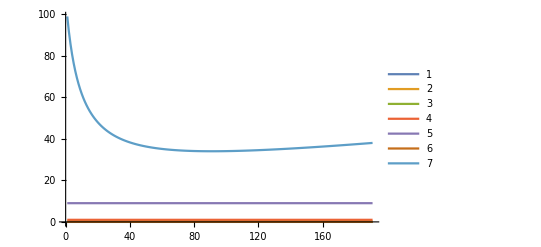

```mathematica
ListPlot[Transpose@Table[vals[t],{t,0.1,2.,.01}],PlotRange->All,PlotLegends->Automatic,Joined->True]
```

```mathematica
(* define ω as the square root of the largest eigenvalue *)
ω[t_]:=Sqrt[(4+9 t+4 t^2+2 √2 √(2+9 t+14 t^2+9 t^3+2 t^4))/t];
```

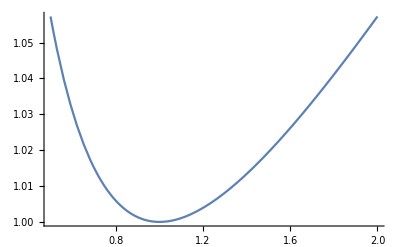

```mathematica
Plot[ω[t]/ω[1.],{t,0.5,2}]
```

```mathematica
(* ω(t=1) is the inflation factor of the AB tiling *)
ω[1]==λ^2
```

True

```mathematica
(* use this for variational equations, since normalization doesn't matter *)
freq[t_]=Eigensystem[T[t]][[2,-1]];
(* use this for frequency computations *)
freqNorm[t_]=Normalize[Eigensystem[T[t]][[2,-1]],Norm[#,1]&];
```

```mathematica
(* when t=1 the coefficients are proportional to the frequencies of local environments *)
freqNorm[1.]
```

{0.0294373,0.0121933,0.0588745,0.0710678,0.0710678,0.343146,0.414214}

Deriving wrt to log t gives access to the moments of the distribution of heights (see notes for details).

```mathematica
(* average height per environment *)
averages=D[Log[freq[E^u]],u]/.u->0//Simplify
```

{5/6-1/(6 √2),1,1/6 (8+√2),1/3 (6+√2),1/3 (3+√2),1/6 (4+√2),0}

```mathematica
(* variance of the distribution of heights (actually diffusion constant) *)
D[Log@(ω[E^u]),{u,2}]/.u->0//Simplify
```

1/(3 √2)

```mathematica
S[u_]:=u b - u^2/(4d)
```

```mathematica
Solve[S'[u]==0,u]
```

{{u→2 b d}}

```mathematica
S[2 b d]
```

b^2 d

```mathematica
d=1/(6 √2);
P[m_,t_]:=1/Sqrt[4 π d t]Exp[-m^2/(4 d t)];
```

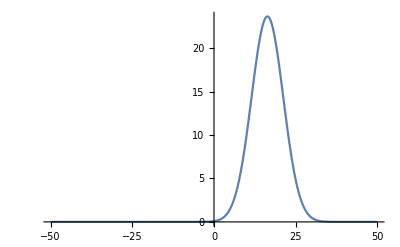

```mathematica
Block[{t=10^2,z=2.},
Plot[z^(m) P[m,t],{m,-t/2,t/2},PlotRange->{All,{0,All}}]]
```

Let us check the numerical sum agrees with the result obtained by Gaussian integration.

```mathematica
NumSum[avm_,t_,z_]:=Sum[z^(m) P[m-avm,t],{m,-t/2,t/2}]
```

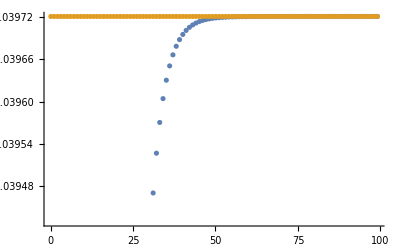

```mathematica
Block[{z=2.,avm=1.5,nums,tTable,th},
tTable=Range[0.1,10^2,1];
nums=Table[Log[NumSum[avm,t,z]]-t d Log[z]^2,{t,tTable}];
th=Table[Log[z^avm ]  ,{t,tTable}];
ListPlot[glue[tTable,#]&/@{nums,th}]
]
```

### IPR

```mathematica
ω[1]//N
```

5.82843

Asymptotic value

```mathematica
(* largest eigenvalue of the inflation matrix T[z] *)
v[z_]:=(4+9z+4 z^2+2 √2 √(2+9 z+14 z^2+9 z^3+2 z^4))/z
```

```mathematica
(* scaling of the IPR *)
CoeffIPR[β_]:=Log[v[β^2]^2/v[β^4]]/Log[v[1]]
```

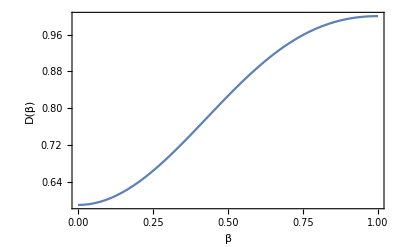

/home/nicolas/git/talks/Oléron 2016/img/coeffPR.pdf

```mathematica
Plot[CoeffIPR[β],{β,0,1},PlotRange->Automatic,Frame->True,FrameLabel->{"β","D(β)"},FrameStyle->st]
Export[NotebookDirectory[]<>"coeffPR.pdf",%]
```

```mathematica
λPavel=1.35809;
CoeffIPR[Sqrt@λPavel]
```

0.987753

```mathematica
1/Sqrt[1.358076]
```

0.8581

```mathematica
0.8581001201827825
```

0.8581

Convergence, variational (nonuiform) local component of the ground state

```mathematica
Cvec={0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864};
```

```mathematica
(* IPR after 2t inflations *)
NonUnifIPR[t_,β_]:=Cvec.Stat[t,β^4]/(Cvec.Stat[t,β^2])^2;
```

```mathematica
tmax=50;
tRange=Range[1,tmax,1];
NonUnifsIPRs=Table[{λ^(4.t),NonUnifIPR[t,βPavel]},{t,tRange}];
ListLogLogPlot[NonUnifsIPRs]
```

-Graphics-

```mathematica
tmin=1;
tmax=7;
dat=Log[NonUnifsIPRs[[tmin;;tmax]]];
fit=LinearModelFit[dat,tt,tt];
Show[ListPlot[dat],Plot[fit[tt],{tt,4tmin Log[λ],4 tmax Log[λ]}],Frame->True,PlotRange->All]
ListPlot[fit["FitResiduals"], Filling->Axis]
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Plot::plln: Limiting value 4\ Log[λ] in {tt, 4\ tmin\ Log[λ], 4\ tmax\ Log[λ]} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in GraphicsBox[List[List[], List[], List[]], List[Rule[DisplayFunction, Identity], Rule[PlotRangePadding, List[List[Scaled[0.02`], Scaled[0.02`]], List[Scaled[0.02`], Scaled[0.05`]]]], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[0, 1], List[0, 1]]], Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[]], Rule[PlotRange, List[List[0, 1], List[0, 1]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[Scaled[0.02`], Scaled[0.02`]], List[Scaled[0.02`], Scaled[0.05`]]]], Rule[Ticks, List[Automatic, Automatic]]]], Plot[fit[tt], {tt, 4 tmin Log[λ], 4 tmax Log[λ]}], Frame → True, PlotRange → All.

Show[-Graphics-,Plot[fit[tt],{tt,4 tmin Log[λ],4 tmax Log[λ]}],Frame→True,PlotRange→All]

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

ListPlot::lpn: LinearModelFit[« 1 »]["FitResiduals"] is not a list of numbers or pairs of numbers.

ListPlot[LinearModelFit[{{Log[λ^4.],Log[{0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^4].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433}/({0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^2].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433})^2]},{Log[λ^8.],Log[{0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^4].T[βPavel^4].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433}/({0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^2].T[βPavel^2].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433})^2]},{Log[λ^12.],Log[{0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^4].T[βPavel^4].T[βPavel^4].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433}/({0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^2].T[βPavel^2].T[βPavel^2].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433})^2]},{Log[λ^16.],Log[{0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^4].T[βPavel^4].T[βPavel^4].T[βPavel^4].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433}/({0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^2].T[βPavel^2].T[βPavel^2].T[βPavel^2].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433})^2]},{Log[λ^20.],Log[{0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^4].T[βPavel^4].T[βPavel^4].T[βPavel^4].T[βPavel^4].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433}/({0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^2].T[βPavel^2].T[βPavel^2].T[βPavel^2].T[βPavel^2].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433})^2]},{Log[λ^24.],Log[{0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^4].T[βPavel^4].T[βPavel^4].T[βPavel^4].T[βPavel^4].T[βPavel^4].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433}/({0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^2].T[βPavel^2].T[βPavel^2].T[βPavel^2].T[βPavel^2].T[βPavel^2].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433})^2]},{Log[λ^28.],Log[{0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^4].T[βPavel^4].T[βPavel^4].T[βPavel^4].T[βPavel^4].T[βPavel^4].T[βPavel^4].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433}/({0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^2].T[βPavel^2].T[βPavel^2].T[βPavel^2].T[βPavel^2].T[βPavel^2].T[βPavel^2].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433})^2]}},tt,tt][FitResiduals],Filling→Axis]

```mathematica
fit
```

LinearModelFit[{{Log[λ^4.],Log[{0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^4].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433}/({0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^2].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433})^2]},{Log[λ^8.],Log[{0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^4].T[βPavel^4].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433}/({0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^2].T[βPavel^2].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433})^2]},{Log[λ^12.],Log[{0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^4].T[βPavel^4].T[βPavel^4].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433}/({0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^2].T[βPavel^2].T[βPavel^2].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433})^2]},{Log[λ^16.],Log[{0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^4].T[βPavel^4].T[βPavel^4].T[βPavel^4].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433}/({0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^2].T[βPavel^2].T[βPavel^2].T[βPavel^2].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433})^2]},{Log[λ^20.],Log[{0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^4].T[βPavel^4].T[βPavel^4].T[βPavel^4].T[βPavel^4].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433}/({0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^2].T[βPavel^2].T[βPavel^2].T[βPavel^2].T[βPavel^2].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433})^2]},{Log[λ^24.],Log[{0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^4].T[βPavel^4].T[βPavel^4].T[βPavel^4].T[βPavel^4].T[βPavel^4].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433}/({0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^2].T[βPavel^2].T[βPavel^2].T[βPavel^2].T[βPavel^2].T[βPavel^2].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433})^2]},{Log[λ^28.],Log[{0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^4].T[βPavel^4].T[βPavel^4].T[βPavel^4].T[βPavel^4].T[βPavel^4].T[βPavel^4].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433}/({0.469686,0.443274,0.416863,0.391146,0.351229,0.286719,0.224864}.T[βPavel^2].T[βPavel^2].T[βPavel^2].T[βPavel^2].T[βPavel^2].T[βPavel^2].T[βPavel^2].{0.894096,0.140454,0.500823,0.888823,0.772367,0.607498,0.59433})^2]}},tt,tt]

### Computation à la Sutherland

Like Sutherland, we associate to each tile (square or lozenge) a labeled corner. We chose here (arbitrarily) the corner which has 2 arrows pointing in. This corresponds to two different corners for the lozenge, but this does not matter as these two corners always have the same height. 
Next, we evaluate L^(l)(h) and S^(l)(h), resp. the number of lozenges/squares having height h at their labeled corner at step l.
We find 
L^(l+1)(-h) = 2L(h) + L(h-1) + 2S(h-1)
S^(l+1)(-h) = 2L(h) + 2L(h-1) + 2S(h-1) + S(h-2)
Therefore, the vector V(h) = (L(h); S(h)) obeys the recursion
V^(l+1)(-h)= A0 V(h) + A1 V(h-1) + A2 V(h-2)
with the A0, A1, A2 matrices given below.

```mathematica
A0={{2,0},{2,0}};
A1={{1,2},{2,2}};
A2={{0,0},{0,1}};
T[z_]:=z^(-2)A2.A0+z^(-1)(A1.A0+A2.A1)+A1.A1+A2.A2+A0.A0+z(A0.A1+A1.A2)+z^2A0.A2;
```

We note that A0+A1+A2={{1,1},{2,1}}^2, the square of the silver mean inflation matrix.

```mathematica
A0+A1+A2//MatrixForm
MatrixPower[{{1,1},{2,1}},2]//MatrixForm
```

(3 | 2
4 | 3)

(3 | 2
4 | 3)

```mathematica
Eigenvalues[T[z]]//Simplify
%/.z->1
```

{9+4/z+4 z-(2 √2 √(z^2 (1+z)^2 (2+5 z+2 z^2)))/z^2,9+4/z+4 z+(2 √2 √(z^2 (1+z)^2 (2+5 z+2 z^2)))/z^2}

{17-12 √2,17+12 √2}

```mathematica
v[z_]:=(4+9z+4 z^2+2 √2 √(2+9 z+14 z^2+9 z^3+2 z^4))/z
```

As for before, we compute the highest eigenvalue of the transformed matrix. We see that it coincides with the previous value.

```mathematica
Simplify[9+4/z+4 z+(2 √2 √(z^2 (1+z)^2 (2+5 z+2 z^2)))/z^2-v[z],Assumptions->z≥0]
```

0

## Variational equations

We want to extremize E({C, β}) = (<ψ|H|ψ>)/(<ψ|ψ>) wrt the 7 variational parameters C_μ (μ = A, B, C, D_1, D_2, E, F), plus β.
If the trial wavefunction writes |ψ> = 1/(√(N^(2l)))Σ_i C_(μ(i))β^(m(i))|i>
then we have
<ψ|ψ> =1/N^(2l) Σ_μ C_μ^2 Σ_m β^(2m)N_μ^(2l)(m)
                           = 1/N^(2l) Σ_μ C_μ^2((Ñ)_μ)^(2l)(β^2)
Now, ((Ñ)_μ)^(2l)(β^2) = ((T(β^2))^l)_(μ,ν)((Ñ)_ν)^(0)(β^2). If the starting vector has a component along the eigenvector associated to the largest eigenvalue of T (which we will assume), then
 ((Ñ)_μ)^(2l)(β^2) =(ω(β^2))^(2l) f_μ(β^2), where ω^2 is the largest eigenvalue of T, and f_μ the corresponding eigenvector.
 We note that (ω(1))^(2l)=N^(2l). Hence
 <ψ|ψ> =((ω(β^2))/(ω(1)))^(2l) Σ_μ C_μ^2 f_μ(β^2)
 The factor (ω(β^2))/(ω(1)) can be incorporated in the normalization of the wf. We will assume it is the case from now on.
 Hence our final expression is
<ψ|ψ> = Σ_μ C_μ^2 f_μ(β^2)

Now, we evaluate
<ψ|H|ψ> =1/N^(2l)Σ_(μ,ν)C_μ C_ν Σ_m β^(2m+ϵ(μ→ν))N_ν(μ,m)
N_ν(μ,m) is the number of bonds (μ,ν) with μ having potential m. ϵ(μ->ν) = ±1 resp if the arrow goes from μ to ν or the reverse.
We can write N_ν(μ,m)=z(ν|μ,m)N_μ(m) with z(ν|μ,m) the average number of type ν site around type μ sites that have potential m.
If the number of ν sites around μ is always the same, then z(ν|μ,m)=z(ν|μ). This is the case for μ < ν (lexicographic order: 1=A, 2=B, 3=C, 4=D_1, 5=D_2, 6=E, 7=F).
Assuming μ < ν, we have
Σ_m β^(2m)N_ν(μ,m)=z(ν|μ)Σ_m β^(2m)N_μ(m)=z(ν|μ)(Ñ)_μ(β^2)
Because the hamiltonian is symmetric, β^(ϵ(μ→ν))N_ν(μ,m) is symmetric under the exchange of μ and ν. In particular, if μ > ν,
β^(ϵ(μ→ν))Σ_m β^(2m)N_ν(μ,m) = β^(ϵ(ν→μ))Σ_m β^(2m)N_μ(ν,m)=β^(ϵ(ν→μ))z(μ|ν)(Ñ)_ν(β^2).
So, we can compute everything, and finally
<ψ|H|ψ> =Σ_(μ,ν)C_μ h_(μ,ν)C_ν
with h_(μ,ν)=β^(ϵ(μ→ν))z(ν|μ)f_μ(β^2) if μ < ν
               = β^(ϵ(ν→μ))z(μ|ν)f_ν(β^2) if μ > ν.

Imposing ∂_C_μ E = 0, we arrive at the 7 equations
h_(μ,ν)C_ν = E C_μ f_μ(β^2) ie
Z_μν C_ν = E C_μ with Z_μν = h_μν/f_μ(β^2)
Therefore, we conclude that C is the eigenvector of Z associated to the eigenvalue E.

The variational Ansatz works for ψ_i of uniform sign (?). So, here since the hopping amplitudes are set to +1, we take the state maximizes E(C).

### Definitions and first tests

```mathematica
Clear[z]
```

```mathematica
For[i=1,i≤9,i++,For[j=1,j≤9,j++,z[i,j]=0]]
```

```mathematica
z[7,1]=8;

z[7,2]=5;
z[6,2]=2;

z[7,3]=2;
z[6,3]=4;

z[7,4]=0;
z[6,4]=4;
z[5,4]=1;

z[7,5]=2;
z[6,5]=2;
z[5,5]=0;

z[7,6]=2;
```

```mathematica
Table[z[i,j],{i,7},{j,7}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 2 | 4 | 4 | 2 | 0 | 0
8 | 5 | 2 | 0 | 2 | 2 | 0)

```mathematica
(* construct the Subscript[h, μν]=β^(ϵ(μ,ν))z(ν|μ)Subscript[f, μ](β^2) matrix *)
hPH[β_,freq_]:=Table[If[i<j,β^Sign[i-j] z[j,i]freq[[i]],β^Sign[j-i] z[i,j]freq[[j]]],{i,7},{j,7}]
```

```mathematica
dfreq[tt_]=D[freq[tt],tt];
```

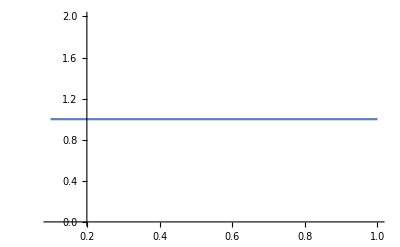

```mathematica
Plot[{freq[t][[-1]]},{t,0.1,1.},PlotRange->All]
```

```mathematica
(* construct the Subscript[δ, β] Subscript[h, μν] matrix *)
dh[β_,freq_,dfreq_]:=Block[{dϵ,df},
dϵ=Table[If[i<j,Sign[i-j] β^(Sign[i-j]-1)z[j,i]freq[[i]],Sign[j-i] β^(Sign[j-i]-1)z[i,j]freq[[j]]],{i,7},{j,7}];
df=Table[If[i<j,β^Sign[i-j] z[j,i]2β dfreq[[i]],β^Sign[j-i] z[i,j]2β dfreq[[j]]],{i,7},{j,7}];
dϵ+df]
```

```mathematica
(* Subscript[h, μν]/Subscript[f, μ] *)
matPH[β_]:=Block[{evalh,evalfreq=freq[β^2]},
evalh=hPH[β,evalfreq];
Table[evalh[[i,j]]/evalfreq[[i]],{i,7},{j,7}]]
(* with Subscript[f, μ] instead of Subscript[f, μ](β^2) *)
matPH2[β_]:=Block[{evalh,evalfreq=freq[1.]},
evalh=hPH[β,evalfreq];
Table[evalh[[i,j]]/evalfreq[[i]],{i,7},{j,7}]]
(* on-site contribution *)
matOS=DiagonalMatrix[{8,7,6,5,5,4,3}];
```

```mathematica
(* return the Subscript[C, μ](i) and E(i), given β *)
CE[β_,t_,indx_]:=Block[{vals,vecs,ord,Emin,C},
{vals,vecs}=Eigensystem[-t matPH[β]+(1-t)matOS];
ord=Ordering[vals];
Emin=(vals[[ord]])[[indx]];
C=(vecs[[ord]])[[indx]];
{C,Emin}
]
```

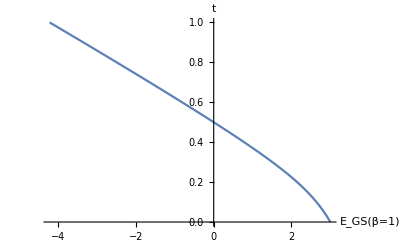

```mathematica
Et=Table[{CE[1.,t,1][[2]],t},{t,0,1,0.01}];
ListPlot[Et,Joined->True,AxesLabel->{"E_GS(β=1)","t"}]
```

```mathematica
(* return the energy associated to Subscript[C, μ] and β *)
En[C_,β_, t_]:=Block[{psiHpsi,psipsi,evalh,evalfreq=freq[β^2]},

evalh=-t hPH[β,evalfreq]+(1-t) matOS evalfreq;
psipsi=C.(DiagonalMatrix[evalfreq].C);
psiHpsi=C.(evalh.C);
psiHpsi/psipsi
]
```

```mathematica
t=1.;
betas=Range[0.1,2.,0.01];
Es=Map[CE[#,t,1][[2]]&,betas];
```

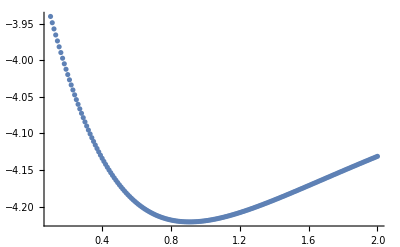

```mathematica
ListPlot[glue[betas,Es],PlotRange->All]
```

```mathematica
Min[Es]
Position[Es,%][[1]]
1/betas[[%[[1]]]]
```

-4.22091

{82}

1.0989

```mathematica
(* return ∂_β<ψ|H|ψ> - E∂_β<ψ|ψ> *)
δβ[β_,t_,indx_]:=Block[{C,E,psidHpsi,psidpsi,evaldfreq,evalD,evalfreq,evalDiag,zvec},
{C,E}=CE[β,t,indx];
evalfreq=freq[β^2];
evaldfreq=dfreq[β^2];
evalD=dh[β,evalfreq,evaldfreq];
zvec={8,7,6,5,5,4,3};
evalDiag=2β DiagonalMatrix[zvec evaldfreq];
psidHpsi=C.((-t evalD+(1-t)evalDiag).C);
psidpsi=C.(2β DiagonalMatrix[evaldfreq].C);
psidHpsi-E*psidpsi
]
```

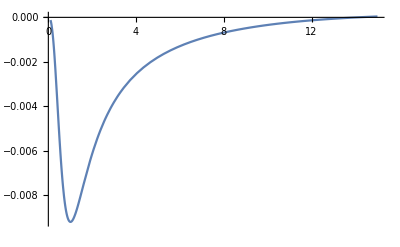

```mathematica
Plot[δβ[β,.4,7],{β,0.1,15},PlotRange->All]
```

### Energies and β, as a function of the hopping parameter, t.

At fixed t, there are

```mathematica
bisec[f_,{a_,b_}]:=If[f[a] f[b]≤0,If[f[(a+b)/2] f[a]≤0,{a,(a+b)/2},If[f[(a+b)/2] f[b]<0,{(a+b)/2,b}]],{0,0}]
linie[f_,{a_,b_},1]={Min[a,b],Max[a,b]};
linie[f_,{a_,b_},n_]:=If[f[a] f[b]≤0,bisec[f,linie[f,{a,b},n-1]],{0,0}]

BisectionMethod[f_,{a_,b_},tol_]:=Block[{evalf,an=a,bn=b},
(* store values of f to speed up computations *)
evalf[x_]:=evalf[x]=f[x];
(* bisect while the root frame is larger than tol *)
While[bn-an≥tol,
{an,bn}=linie[evalf,{an,bn},2]];
{an,bn}]
```

```mathematica
t=0.5;
BisectionMethod[δβ[#,t,1]&,{0.8,1.3},10^-6]
```

{1.,1.}

```mathematica
FindBeta[t_,indx_,{βa_,βb_},tol_]:=Block[{β1,β2},
{β1,β2}=BisectionMethod[δβ[#,t,indx]&,{βa,βb},tol];
(β1+β2)/2]
```

Finding β for the groundstate

```mathematica
ts=Range[0,1,0.02];
betasMin=Table[FindBeta[t,1,{0.00001,1.2},10^(-6)],{t,ts}];
```

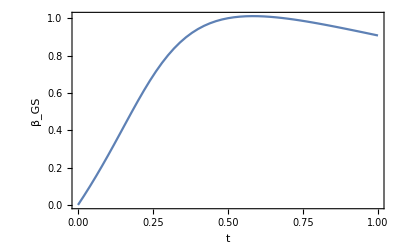

```mathematica
ListPlot[glue[ts,betasMin],PlotRange->All,Joined->True,FrameLabel->stylize/@{"t","β_GS"},FrameStyle->st,Frame->True]
```

```mathematica
Export[NotebookDirectory[]<>"beta_t.pdf",%]
```

/home/nicolas/git/gaps_topology/Ammann-Beenker/beta_t.pdf

Finding β for the 7th excited state.
It seems that β diverges as t → 0.

```mathematica
ts=Range[0,0.5,0.01];
betasMin=Table[FindBeta[t,7,{4.,500.},10^(-6)],{t,ts}];
```

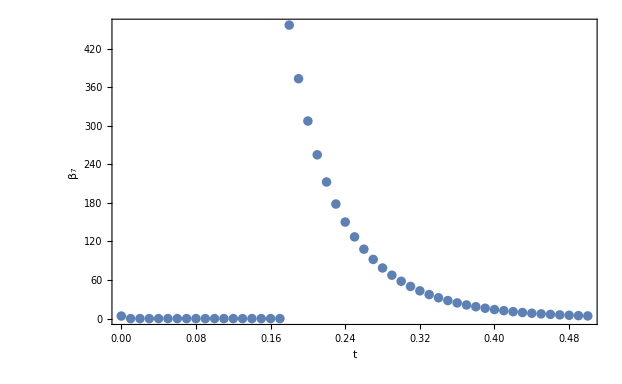

```mathematica
ListPlot[glue[ts,betasMin],PlotRange->All,Joined->False,FrameLabel->stylize/@{"t","β_7"},FrameStyle->st,Frame->True]
```

Let us define γ = 1/β. 
We note that for some states (eg here the 7th one) γ → 0 as t → 0.

```mathematica
δγ[γ_,t_,indx_]:=δβ[1/γ,t,indx];
```

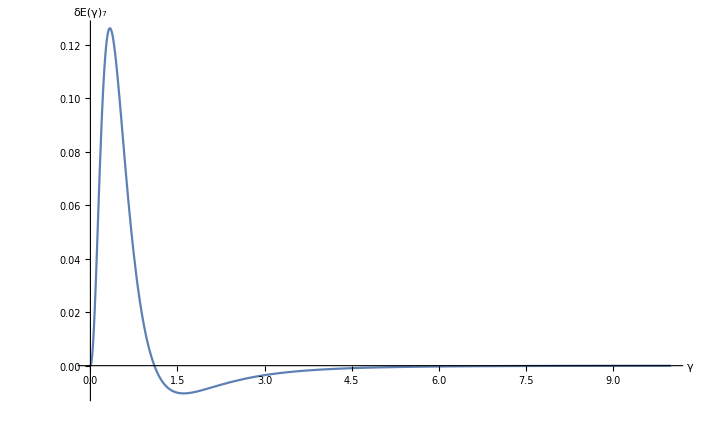

```mathematica
Plot[δγ[γ,1.,1],{γ,-0.01,10.},PlotRange->All,AxesLabel->stylize/@{"γ","δE(γ)_7"}]
```

```mathematica
FindGamma[t_,indx_,{γa_,γb_},tol_]:=Block[{γ1,γ2},
{γ1,γ2}=BisectionMethod[δγ[#,t,indx]&,{γa,γb},tol];
(γ1+γ2)/2]
```

```mathematica
FindGamma[.2,7,{0.0001,0.01},10^-6]
```

0.00325508

```mathematica
ts=Range[0,1.,0.05];
gammasMin=Table[FindGamma[t,2,{10^(-4),10.},10^-6],{t,ts}];
```

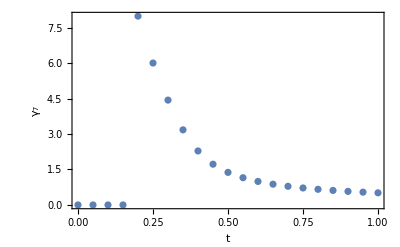

```mathematica
ListPlot[glue[ts,gammasMin],PlotRange->All,Joined->False,FrameLabel->stylize/@{"t","γ_7"},FrameStyle->st,Frame->True]
```

Some observations:
i = 1:	β behaves nicely
i = 2:	
i = 3:	γ behaves nicely but goes neither to 0 nor to ∞ at t = 0
i = 4:	there are several solutions for β: at least β_1 and β_2, β_1<β_2 and β_1→0 as t→1/2 and β_2→∞ as t→0.25
i = 5:
i = 6:
i = 7:	γ behaves nicely

```mathematica
ts=Range[0,1.,0.05];
gammasMin=Table[FindGamma[t,3,{0.01,10.},10^-6],{t,ts}];
```

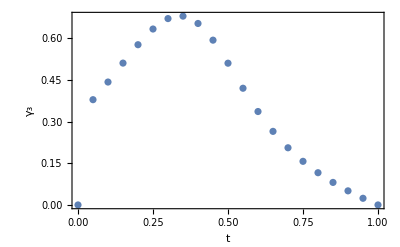

```mathematica
ListPlot[glue[ts,gammasMin],PlotRange->All,Joined->False,FrameLabel->stylize/@{"t","γ_3"},FrameStyle->st,Frame->True]
```

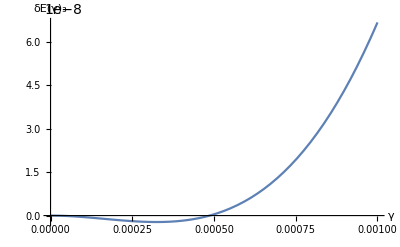

```mathematica
Plot[δγ[γ,.257,4],{γ,0.,.001},PlotRange->All,AxesLabel->stylize/@{"γ","δE(γ)_3"}]
```

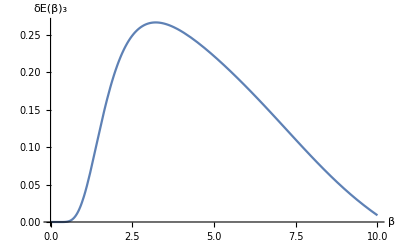

```mathematica
Plot[δβ[β,.3,4],{β,0.,10},PlotRange->All,AxesLabel->stylize/@{"β","δE(β)_3"}]
```

```mathematica
ts=Range[0,1.,0.1];
gammasMin=Table[FindGamma[t,4,{10^(-8),2.},10^-6],{t,ts}];
```

```mathematica
ListPlot[glue[ts,gammasMin],PlotRange->All,Joined->False,FrameLabel->stylize/@{"t","γ_7"},FrameStyle->st,Frame->True]
```

```mathematica
ts=Range[0,.5,0.01];
betasMin=Table[FindBeta[t,4,{10^(-8),2.},10^-6],{t,ts}];
```

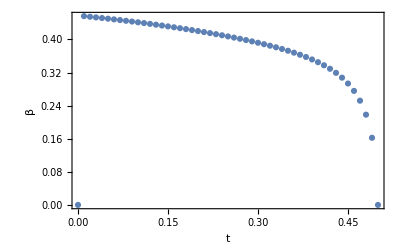

$Aborted

```mathematica
ListPlot[glue[ts,betasMin],PlotRange->All,Joined->False,FrameLabel->stylize/@{"t","β"},FrameStyle->st,Frame->True]
```